```mathematica
$Assumptions={X>0,n>0,a>0,d>0,q>0,t>0,z>0,w>0,α>0,β>0,σ>0,s>0,h>0,m>0,,z∈ Reals,px2∈ Reals,py2∈ Reals,px1∈ Reals,py1∈ Reals,px∈ Reals,py∈ Reals,r∈ Reals,r1∈ Reals,r2∈ Reals,x1∈ Reals,x2∈ Reals,x∈ Reals,w∈ Reals,t∈ Reals,k1∈ Reals,k2∈ Reals,k∈ Reals,n∈ Reals,q∈ Reals,a∈ Reals,d∈ Reals,p∈ Reals,p1∈ Reals,p2∈ Reals,y1∈Reals,y2∈Reals,α∈Reals,β∈Reals,σ∈Reals,s∈Reals,v1∈Reals,v2∈Reals,β1∈Reals,β2∈Reals,X∈Reals,h∈Reals,m∈
Reals}
```

{X>0,n>0,a>0,d>0,q>0,t>0,z>0,w>0,α>0,β>0,σ>0,s>0,h>0,m>0,Null,z∈Reals,px2∈Reals,py2∈Reals,px1∈Reals,py1∈Reals,px∈Reals,py∈Reals,r∈Reals,r1∈Reals,r2∈Reals,x1∈Reals,x2∈Reals,x∈Reals,w∈Reals,t∈Reals,k1∈Reals,k2∈Reals,k∈Reals,n∈Reals,q∈Reals,a∈Reals,d∈Reals,p∈Reals,p1∈Reals,p2∈Reals,y1∈Reals,y2∈Reals,α∈Reals,β∈Reals,σ∈Reals,s∈Reals,v1∈Reals,v2∈Reals,β1∈Reals,β2∈Reals,X∈Reals,h∈Reals,m∈Reals}

```mathematica
cXStart=-100;
cXStep=0.1;
cXLength= 2000;
cTStep="1.0e-4";
cTStepint = 0.00001;
cTLength="1000000";
cTLengthint=1000000;
cep=0.98;
ccuts=10;
csigma=1;
cdslit=3.0;
```

```mathematica
√π
```

```mathematica
(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) σ)^(-1/2)
```

```mathematica
1/(√(2 √(2π)(1+ⅇ^(-d^2/(2 σ^2))) σ))
```

1/(2^(3/4) π^(1/4) √((1+ⅇ^(-d^2/(2 σ^2))) σ))

```mathematica
Integrate[(1/(√(2 √(2π)(1+ⅇ^(-d^2/(2 σ^2))) σ))(ⅇ^(-(d-x)^2/(4 σ^2))+ⅇ^(-(d+x)^2/(4 σ^2))))^2,{x,-∞,∞}]
```

1

```mathematica
Integrate[(ⅇ^(-(d-x)^2/(4 σ^2))+ⅇ^(-(d+x)^2/(4 σ^2)))ⅇ^(ⅈ x p/h),{x,-∞,∞}]
```

2 ⅇ^(-(p (ⅈ d h+p σ^2))/h^2) (1+ⅇ^((2 ⅈ d p)/h)) √π σ

```mathematica
Integrate[(ⅇ^(-(d-x)^2/(4 σ^2))+ⅇ^(-(d+x)^2/(4 σ^2)))ⅇ^(-(z)^2/(4 σ^2))ⅇ^(ⅈ pz0 z)ⅇ^(ⅈ (px x+pz z)),{x,-∞,∞},{z,-∞,∞}]
```

```mathematica
ⅇ^(-(px^2+(pz+pz0)^2) σ^2) (Cos[d px])
```

```mathematica
ⅇ^(-p^2 σ^2) Cos[d p]
```

ⅇ^(-p^2 σ^2) Cos[d p]

```mathematica
Integrate[ⅇ^(ⅈ (-a p^2 t+p x)) ⅇ^(-p^2 σ^2) Cos[d p],{p,-∞,∞}]
```

```mathematica
(ⅇ^((ⅈ (d^2+x^2))/(2 a t-2 ⅈ σ^2)) (ⅇ^((d-x)^2/(4 (ⅈ a t+σ^2)))+ⅇ^((d+x)^2/(4 (ⅈ a t+σ^2)))) √π)/(2 √(ⅈ a t+σ^2))
```

```mathematica
ⅇ^((d-x)^2/(4 (-ⅈ a t+σ^2)))ⅇ^((d+x)^2/(4 (-ⅈ a t+σ^2)))
```

```mathematica
Simplify[ⅇ^((d-x)^2/(4 (-ⅈ a t+σ^2)))ⅇ^((d-x)^2/(4 (ⅈ a t+σ^2)))]+Simplify[ⅇ^((d+x)^2/(4 (-ⅈ a t+σ^2)))ⅇ^((d+x)^2/(4 (ⅈ a t+σ^2)))]+Simplify[ⅇ^((d-x)^2/(4 (ⅈ a t+σ^2)))ⅇ^((d+x)^2/(4 (-ⅈ a t+σ^2)))]+Simplify[ⅇ^((d-x)^2/(4 (-ⅈ a t+σ^2)))ⅇ^((d+x)^2/(4 (ⅈ a t+σ^2)))]
```

ⅇ^(((d-x)^2 σ^2)/(2 (a^2 t^2+σ^4)))+ⅇ^(((d+x)^2 σ^2)/(2 (a^2 t^2+σ^4)))+ⅇ^((-2 ⅈ a d t x+(d^2+x^2) σ^2)/(2 (a^2 t^2+σ^4)))+ⅇ^((2 ⅈ a d t x+(d^2+x^2) σ^2)/(2 (a^2 t^2+σ^4)))

```mathematica
Integrate[ⅇ^(ⅈ (-a p^2 t+p z)) ⅇ^(-(p+v)^2 σ^2) ,{p,-∞,∞}]
```

(ⅇ^((ⅈ z^2-4 v (a t v+z) σ^2)/(4 a t-4 ⅈ σ^2)) √π)/(√(ⅈ a t+σ^2))

```mathematica
FullSimplify[(ⅈ z^2-4 v (a t v+z) σ^2)/(4 a t-4 ⅈ σ^2)]
```

```mathematica
(- z^2-ⅈ 4 v (a t v+z) σ^2)/(ⅈ 4 a t+4 σ^2)
```

```mathematica
(-z^2/σ^2-4 ⅈ  (v a t v+z v))/(4 (ⅈ a t/σ^2+1))
```

```mathematica
(-4 ⅈ ((h/(2m)) t p0^2+p0 z)-z^2/σ^2)/(4 (1+(ⅈ (h/(2m)) t)/σ^2))
```

(-4 ⅈ ((h p0^2 t)/(2 m)+p0 z)-z^2/σ^2)/(4 (1+(ⅈ h t)/(2 m σ^2)))

```mathematica
(-4 ⅈ ((h p0^2 t)/(2 m)+p0 z)σ^2-z^2)/(4 (σ^2+(ⅈ h t)/(2 m)))
```

(-z^2-4 ⅈ ((h p0^2 t)/(2 m)+p0 z) σ^2)/(4 ((ⅈ h t)/(2 m)+σ^2))

```mathematica
FullSimplify[(ⅈ z^2-4 v (a t v+z) σ^2)/(4 a t-4 ⅈ σ^2)+(-ⅈ z^2-4 v (a t v+z) σ^2)/(4 a t+4 ⅈ σ^2)]
```

-((2 a t v+z)^2 σ^2)/(2 (a^2 t^2+σ^4))

```mathematica
Simplify[(-4 ⅈ ((h p0^2 t)/(2 m)+p0 z)-z^2/σ^2)/(4 (1+(ⅈ h t)/(2 m σ^2)))+(4 ⅈ ((h p0^2 t)/(2 m)+p0 z)-z^2/σ^2)/(4 (1-(ⅈ h t)/(2 m σ^2)))]
```

-(2 (h p0 t+m z)^2 σ^2)/(h^2 t^2+4 m^2 σ^4)

```mathematica
-(2 ((h/(2 m)) p0 t+z)^2)/(h^2 t^2/(σ^2)4 m^2+ σ^2)
```

-(2 ((h p0 t)/(2 m)+z)^2)/((4 h^2 m^2 t^2)/σ^2+σ^2)

```mathematica
Simplify[1/(4 (1+(ⅈ h t)/(2 m σ^2)))+1/(4 (1-(ⅈ h t)/(2 m σ^2)))]
```

(2 m^2 σ^4)/(h^2 t^2+4 m^2 σ^4)

```mathematica
Integrate[ⅇ^(ⅈ (-(h t)/(2 m)(px^2+pz^2)+px x + pz z)) ⅇ^((-px^2-(pz+pz0)^2) σ^2) Cos[d px],{px,-∞,∞},{pz,-∞,∞}]
```

(ⅇ^((ⅈ (2 d^2 m+2 ⅈ h pz0^2 t σ^2+m (2 x^2+z^2+4 ⅈ pz0 z σ^2)))/(2 h t-4 ⅈ m σ^2)) (ⅇ^((m (d-x)^2)/(2 ⅈ h t+4 m σ^2))+ⅇ^((m (d+x)^2)/(2 ⅈ h t+4 m σ^2))) m π)/(ⅈ h t+2 m σ^2)

```mathematica
Integrate[(σ ((ⅇ^(-((d-x)^2 σ^2)/(4 (a^2 t^2+σ^4)))+ⅇ^(-((d+x)^2 σ^2)/(4 (a^2 t^2+σ^4))))^2-4 ⅇ^(-((d^2+x^2) σ^2)/(2 (a^2 t^2+σ^4))) Sin[(a d t x)/(2 (a^2 t^2+σ^4))]^2))/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(a^2 t^2+σ^4)),{x,-∞,∞}]
```

1

```mathematica
√(σ/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(ⅈ a t+σ^2)))
```

(√(σ/((1+ⅇ^(-d^2/(2 σ^2))) √(ⅈ a t+σ^2))))/(2^(3/4) π^(1/4))

```mathematica
√(σ/(2 √(2 π)(1+ⅇ^(-d^2/(2 σ^2))) √(ⅈ a t+σ^2)))
```

```mathematica
Simplify[√(σ/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(ⅈ a t+σ^2)))√(σ/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(-ⅈ a t+σ^2)))]
```

σ/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) (a^2 t^2+σ^4)^(1/4))

```mathematica
√(σ/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(a^2 t^2+σ^4)))
```

(√(σ/((1+ⅇ^(-d^2/(2 σ^2))) √(a^2 t^2+σ^4))))/(2^(3/4) π^(1/4))

```mathematica
Rf[x_,t_,d_,σ_,a_]:=(σ ((ⅇ^(-((d-x)^2 σ^2)/(4 (a^2 t^2+σ^4)))+ⅇ^(-((d+x)^2 σ^2)/(4 (a^2 t^2+σ^4))))^2-4 ⅇ^(-((d^2+x^2) σ^2)/(2 (a^2 t^2+σ^4))) Sin[(a d t x)/(2 (a^2 t^2+σ^4))]^2))/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(a^2 t^2+σ^4))
```

```mathematica
(σ ((ⅇ^(-((d-x)^2 σ^2)/(4 (a^2 t^2+σ^4)))+ⅇ^(-((d+x)^2 σ^2)/(4 (a^2 t^2+σ^4))))^2-4 ⅇ^(-((d^2+x^2) σ^2)/(2 (a^2 t^2+σ^4))) Sin[(a d t x)/(2 (a^2 t^2+σ^4))]^2))/(2 (1+ⅇ^(-d^2/(2 σ^2))) √(2 π) √(a^2 t^2+σ^4))
```

```mathematica
FileLists=0;
FileLists=ReadList["/Users/cricha5/Desktop/Physics/SchrodOrigins/ChrisFiniteDifferenceTransitionOMP/ChrisFiniteDifferenceTransitionOMP/probdata_ep-10.dat",Number,RecordLists->True];
FileLists2=0;
FileLists2=ReadList["/Users/cricha5/Desktop/Physics/SchrodOrigins/ChrisFiniteDifferenceTransitionOMP/ChrisFiniteDifferenceTransitionOMP/probdata_ep-98.dat",Number,RecordLists->True];
FileLists3=0;
FileLists3=ReadList["/Users/cricha5/Desktop/Physics/SchrodOrigins/ChrisFiniteDifferenceTransitionOMP/ChrisFiniteDifferenceTransitionOMP/probdata_ep-95.dat",Number,RecordLists->True];
FileLists4=0;
FileLists4=ReadList["/Users/cricha5/Desktop/Physics/SchrodOrigins/ChrisFiniteDifferenceTransitionOMP/ChrisFiniteDifferenceTransitionOMP/probdata_ep-8.dat",Number,RecordLists->True];
FileLists5=0;
FileLists5=ReadList["/Users/cricha5/Desktop/Physics/SchrodOrigins/ChrisFiniteDifferenceTransitionOMP/ChrisFiniteDifferenceTransitionOMP/probdata_ep-4.dat",Number,RecordLists->True];
FileLists6=0;
FileLists6=ReadList["/Users/cricha5/Desktop/Physics/SchrodOrigins/ChrisFiniteDifferenceTransitionOMP/ChrisFiniteDifferenceTransitionOMP/probdata_ep-0.dat",Number,RecordLists->True];
```

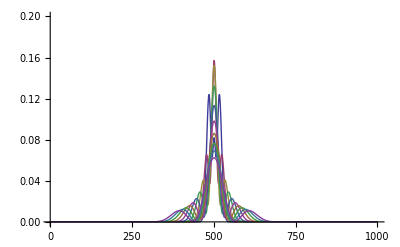

```mathematica
ListLinePlot[FileLists,PlotRange->{Full,{0,0.2}}]
```

```mathematica
Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-1.0)],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->Orange,Frame->True,Axes->False,FrameLabel->{"x/σ","σ|ψ|"^2}, RotateLabel->False],ListLinePlot[FileLists⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->{Black,Dashing[Large],Thickness[.005]}],LabelStyle->Directive[FontSize->18]]
```

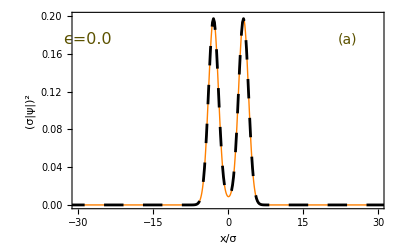

```mathematica
Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-0.98)],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->Orange,Frame->True,Axes->False,FrameLabel->{"x/σ","σ|ψ|"^2}, RotateLabel->False],ListLinePlot[FileLists2⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->{Black,Dashing[Large],Thickness[.005]}],LabelStyle->Directive[FontSize->18]]
```

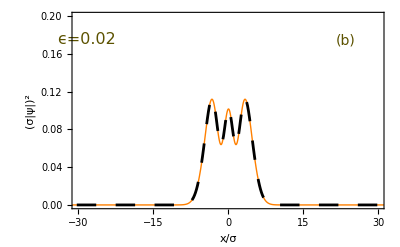

```mathematica
Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-0.95)],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->Orange,Frame->True,Axes->False,FrameLabel->{"x/σ","σ|ψ|"^2}, RotateLabel->False],ListLinePlot[FileLists3⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->{Black,Dashing[Large],Thickness[.005]}],LabelStyle->Directive[FontSize->18]]
```

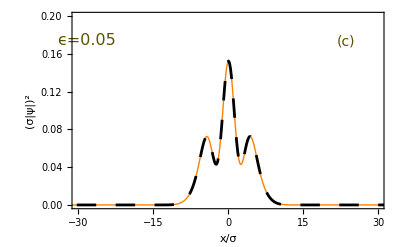

```mathematica
Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-0.8)],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->Orange,Frame->True,Axes->False,FrameLabel->{"x/σ","σ|ψ|"^2}, RotateLabel->False],ListLinePlot[FileLists4⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->{Black,Dashing[Large],Thickness[.005]}],LabelStyle->Directive[FontSize->18]]
```

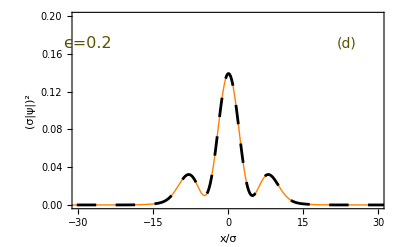

```mathematica
Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-0.4)],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->Orange,Frame->True,Axes->False,FrameLabel->{"x/σ","σ|ψ|"^2}, RotateLabel->False],ListLinePlot[FileLists5⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->{Black,Dashing[Large],Thickness[.005]}],LabelStyle->Directive[FontSize->18]]
```

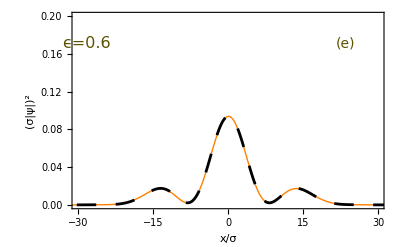

```mathematica
Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-0.0)],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->Orange,Frame->True,Axes->False,FrameLabel->{"x/σ","σ|ψ|"^2}, RotateLabel->False],ListLinePlot[FileLists6⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.2}},PlotStyle->{Black,Dashing[Large],Thickness[.005]}],LabelStyle->Directive[FontSize->18]]
```

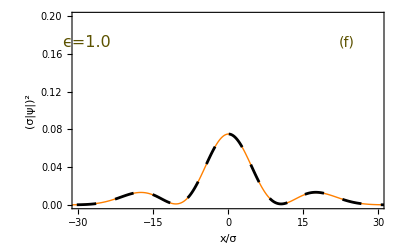

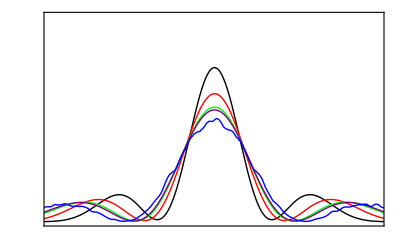

```mathematica
Show[Plot[Rf[(x-cXStep), (cTStepint (cTLengthint-1)) ,cdslit,csigma,√(1-cep)1.0],{x,cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.1}},PlotStyle->Black,Frame->True,Axes->False,FrameTicks->None],ListLinePlot[FileLists⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.1}},PlotStyle->Red,Frame->True,Axes->False],ListLinePlot[FileLists2⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.1}},PlotStyle->Green,Frame->True,Axes->False],ListLinePlot[FileLists3⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.1}},PlotStyle->Purple,Frame->True,Axes->False],ListLinePlot[FileLists4⟦ccuts, All⟧, DataRange->{cXStart,cXStart + cXStep cXLength},PlotRange->{{-30,30},{0,0.1}},PlotStyle->Blue,Frame->True,Axes->False]]
```